```mathematica
(*
衰变过程:
 Rn222 -> Po218 -> Pb214 -> Bi214 -> Po214 -> Po210

1. Rn222 半衰期3.824day α粒子能量 5.49MeV
2. Po218 半衰期3.04min  α粒子能量 6.00MeV
3. Pb214 半衰期26.8min  β,γ
4. Bi214 半衰期19.7min  β,γ
5. Po214 半衰期164us  α粒子能量 7.69MeV
6. Po210 半衰期138.8day α粒子能量 5.30MeV
*)
```

```mathematica
DSolve[{a'[t]==-k1*a[t],b'[t]==k1*a[t]-k2*b[t],c'[t]==k2*b[t]-k3*c[t],d'[t]==k3*c[t]-k4*d[t],e'[t]==k4*d[t]},{a[t],b[t],c[t],d[t],e[t]},t]
```

{{a[t]→ⅇ^(-k1 t) C[1],b[t]→-(ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t)+ⅇ^(k2 t)) k1 C[1])/(k1-k2)+ⅇ^(-k2 t) C[2],c[t]→(ⅇ^(-k1 t-k2 t-k3 t) k1 k2 (ⅇ^(k1 t+k2 t) k1-ⅇ^(k1 t+k3 t) k1-ⅇ^(k1 t+k2 t) k2+ⅇ^(k2 t+k3 t) k2+ⅇ^(k1 t+k3 t) k3-ⅇ^(k2 t+k3 t) k3) C[1])/((k1-k2) (k1-k3) (k2-k3))-(ⅇ^(-k2 t-k3 t) (-ⅇ^(k2 t)+ⅇ^(k3 t)) k2 C[2])/(k2-k3)+ⅇ^(-k3 t) C[3],d[t]→1/((-k1+k2) (k1-k3) (k2-k3) (k1-k4) (k2-k4) (k3-k4))ⅇ^(-k1 t-k2 t-k3 t-k4 t) k1 k2 k3 (-ⅇ^(k1 t+k2 t+k3 t) k1^2 k2+ⅇ^(k1 t+k2 t+k4 t) k1^2 k2+ⅇ^(k1 t+k2 t+k3 t) k1 k2^2-ⅇ^(k1 t+k2 t+k4 t) k1 k2^2+ⅇ^(k1 t+k2 t+k3 t) k1^2 k3-ⅇ^(k1 t+k3 t+k4 t) k1^2 k3-ⅇ^(k1 t+k2 t+k3 t) k2^2 k3+ⅇ^(k2 t+k3 t+k4 t) k2^2 k3-ⅇ^(k1 t+k2 t+k3 t) k1 k3^2+ⅇ^(k1 t+k3 t+k4 t) k1 k3^2+ⅇ^(k1 t+k2 t+k3 t) k2 k3^2-ⅇ^(k2 t+k3 t+k4 t) k2 k3^2-ⅇ^(k1 t+k2 t+k4 t) k1^2 k4+ⅇ^(k1 t+k3 t+k4 t) k1^2 k4+ⅇ^(k1 t+k2 t+k4 t) k2^2 k4-ⅇ^(k2 t+k3 t+k4 t) k2^2 k4-ⅇ^(k1 t+k3 t+k4 t) k3^2 k4+ⅇ^(k2 t+k3 t+k4 t) k3^2 k4+ⅇ^(k1 t+k2 t+k4 t) k1 k4^2-ⅇ^(k1 t+k3 t+k4 t) k1 k4^2-ⅇ^(k1 t+k2 t+k4 t) k2 k4^2+ⅇ^(k2 t+k3 t+k4 t) k2 k4^2+ⅇ^(k1 t+k3 t+k4 t) k3 k4^2-ⅇ^(k2 t+k3 t+k4 t) k3 k4^2) C[1]+(ⅇ^(-k2 t-k3 t-k4 t) k2 k3 (ⅇ^(k2 t+k3 t) k2-ⅇ^(k2 t+k4 t) k2-ⅇ^(k2 t+k3 t) k3+ⅇ^(k3 t+k4 t) k3+ⅇ^(k2 t+k4 t) k4-ⅇ^(k3 t+k4 t) k4) C[2])/((k2-k3) (k2-k4) (k3-k4))-(ⅇ^(-k3 t-k4 t) (-ⅇ^(k3 t)+ⅇ^(k4 t)) k3 C[3])/(k3-k4)+ⅇ^(-k4 t) C[4],e[t]→-1/((-k1+k2) (k1-k3) (k2-k3) (k1-k4) (k2-k4) (k3-k4))ⅇ^(-k1 t-k2 t-k3 t-k4 t) (-ⅇ^(k1 t+k2 t+k3 t) k1^3 k2^2 k3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2^2 k3+ⅇ^(k1 t+k2 t+k3 t) k1^2 k2^3 k3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2^3 k3+ⅇ^(k1 t+k2 t+k3 t) k1^3 k2 k3^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2 k3^2-ⅇ^(k1 t+k2 t+k3 t) k1 k2^3 k3^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^3 k3^2-ⅇ^(k1 t+k2 t+k3 t) k1^2 k2 k3^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2 k3^3+ⅇ^(k1 t+k2 t+k3 t) k1 k2^2 k3^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^2 k3^3+ⅇ^(k1 t+k2 t+k4 t) k1^3 k2^2 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2^2 k4-ⅇ^(k1 t+k2 t+k4 t) k1^2 k2^3 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2^3 k4-ⅇ^(k1 t+k3 t+k4 t) k1^3 k3^2 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k3^2 k4+ⅇ^(k2 t+k3 t+k4 t) k2^3 k3^2 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^3 k3^2 k4+ⅇ^(k1 t+k3 t+k4 t) k1^2 k3^3 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k3^3 k4-ⅇ^(k2 t+k3 t+k4 t) k2^2 k3^3 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^2 k3^3 k4-ⅇ^(k1 t+k2 t+k4 t) k1^3 k2 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2 k4^2+ⅇ^(k1 t+k2 t+k4 t) k1 k2^3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^3 k4^2+ⅇ^(k1 t+k3 t+k4 t) k1^3 k3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k3 k4^2-ⅇ^(k2 t+k3 t+k4 t) k2^3 k3 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^3 k3 k4^2-ⅇ^(k1 t+k3 t+k4 t) k1 k3^3 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k3^3 k4^2+ⅇ^(k2 t+k3 t+k4 t) k2 k3^3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2 k3^3 k4^2+ⅇ^(k1 t+k2 t+k4 t) k1^2 k2 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2 k4^3-ⅇ^(k1 t+k2 t+k4 t) k1 k2^2 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^2 k4^3-ⅇ^(k1 t+k3 t+k4 t) k1^2 k3 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k3 k4^3+ⅇ^(k2 t+k3 t+k4 t) k2^2 k3 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^2 k3 k4^3+ⅇ^(k1 t+k3 t+k4 t) k1 k3^2 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k3^2 k4^3-ⅇ^(k2 t+k3 t+k4 t) k2 k3^2 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2 k3^2 k4^3) C[1]+(ⅇ^(-k2 t-k3 t-k4 t) (-ⅇ^(k2 t+k3 t) k2^2 k3+ⅇ^(k2 t+k3 t+k4 t) k2^2 k3+ⅇ^(k2 t+k3 t) k2 k3^2-ⅇ^(k2 t+k3 t+k4 t) k2 k3^2+ⅇ^(k2 t+k4 t) k2^2 k4-ⅇ^(k2 t+k3 t+k4 t) k2^2 k4-ⅇ^(k3 t+k4 t) k3^2 k4+ⅇ^(k2 t+k3 t+k4 t) k3^2 k4-ⅇ^(k2 t+k4 t) k2 k4^2+ⅇ^(k2 t+k3 t+k4 t) k2 k4^2+ⅇ^(k3 t+k4 t) k3 k4^2-ⅇ^(k2 t+k3 t+k4 t) k3 k4^2) C[2])/((k2-k3) (k2-k4) (k3-k4))+(ⅇ^(-k3 t-k4 t) (ⅇ^(k3 t) k3-ⅇ^(k3 t+k4 t) k3-ⅇ^(k4 t) k4+ⅇ^(k3 t+k4 t) k4) C[3])/(-k3+k4)+ⅇ^(-k4 t) (-1+ⅇ^(k4 t)) C[4]+C[5]}}

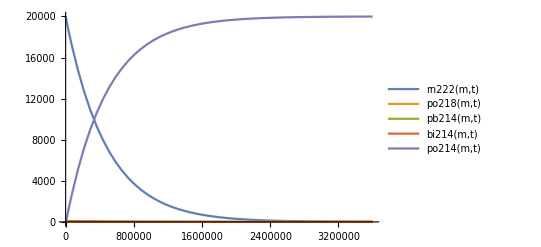

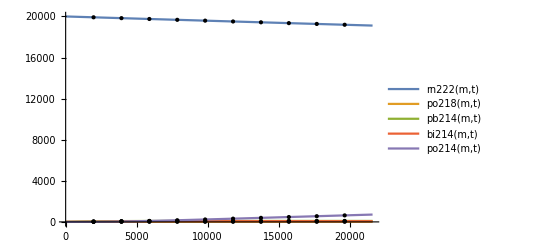

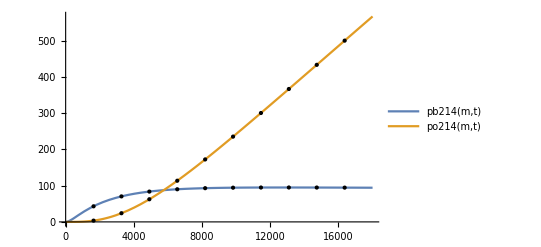

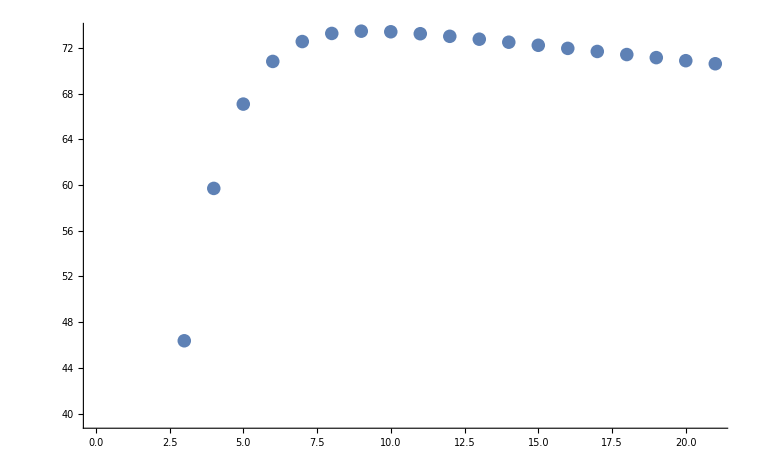

```mathematica
(*
 1. 假设初始注入nBq的Rn222
2. 忽略注入Rn222中的衰变子体数量
3. Rn222衰变子体数量随时间t变化关系如下
*)
k1 = Log[2]/(3.82*24*60*60);
k2 = Log[2]/(3.01*60);
k3 = Log[2]/(26.8*60);
k4 = Log[2]/(19.9*60);
rn222[n_,t_]:=ⅇ^(-k1 t) n;
po218[n_,t_]:=-(ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t)+ⅇ^(k2 t)) k1 n)/(k1-k2);
pb214[n_,t_]:=(ⅇ^(-k1 t-k2 t-k3 t) k1 k2 (ⅇ^(k1 t+k2 t) k1-ⅇ^(k1 t+k3 t) k1-ⅇ^(k1 t+k2 t) k2+ⅇ^(k2 t+k3 t) k2+ⅇ^(k1 t+k3 t) k3-ⅇ^(k2 t+k3 t) k3) n)/((k1-k2) (k1-k3) (k2-k3));
bi214[n_,t_] := 1/((-k1+k2) (k1-k3) (k2-k3) (k1-k4) (k2-k4) (k3-k4))ⅇ^(-k1 t-k2 t-k3 t-k4 t) k1 k2 k3 (-ⅇ^(k1 t+k2 t+k3 t) k1^2 k2+ⅇ^(k1 t+k2 t+k4 t) k1^2 k2+ⅇ^(k1 t+k2 t+k3 t) k1 k2^2-ⅇ^(k1 t+k2 t+k4 t) k1 k2^2+ⅇ^(k1 t+k2 t+k3 t) k1^2 k3-ⅇ^(k1 t+k3 t+k4 t) k1^2 k3-ⅇ^(k1 t+k2 t+k3 t) k2^2 k3+ⅇ^(k2 t+k3 t+k4 t) k2^2 k3-ⅇ^(k1 t+k2 t+k3 t) k1 k3^2+ⅇ^(k1 t+k3 t+k4 t) k1 k3^2+ⅇ^(k1 t+k2 t+k3 t) k2 k3^2-ⅇ^(k2 t+k3 t+k4 t) k2 k3^2-ⅇ^(k1 t+k2 t+k4 t) k1^2 k4+ⅇ^(k1 t+k3 t+k4 t) k1^2 k4+ⅇ^(k1 t+k2 t+k4 t) k2^2 k4-ⅇ^(k2 t+k3 t+k4 t) k2^2 k4-ⅇ^(k1 t+k3 t+k4 t) k3^2 k4+ⅇ^(k2 t+k3 t+k4 t) k3^2 k4+ⅇ^(k1 t+k2 t+k4 t) k1 k4^2-ⅇ^(k1 t+k3 t+k4 t) k1 k4^2-ⅇ^(k1 t+k2 t+k4 t) k2 k4^2+ⅇ^(k2 t+k3 t+k4 t) k2 k4^2+ⅇ^(k1 t+k3 t+k4 t) k3 k4^2-ⅇ^(k2 t+k3 t+k4 t) k3 k4^2) n;
po214[n_,t_]:=-1/((-k1+k2) (k1-k3) (k2-k3) (k1-k4) (k2-k4) (k3-k4))ⅇ^(-k1 t-k2 t-k3 t-k4 t) (-ⅇ^(k1 t+k2 t+k3 t) k1^3 k2^2 k3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2^2 k3+ⅇ^(k1 t+k2 t+k3 t) k1^2 k2^3 k3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2^3 k3+ⅇ^(k1 t+k2 t+k3 t) k1^3 k2 k3^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2 k3^2-ⅇ^(k1 t+k2 t+k3 t) k1 k2^3 k3^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^3 k3^2-ⅇ^(k1 t+k2 t+k3 t) k1^2 k2 k3^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2 k3^3+ⅇ^(k1 t+k2 t+k3 t) k1 k2^2 k3^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^2 k3^3+ⅇ^(k1 t+k2 t+k4 t) k1^3 k2^2 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2^2 k4-ⅇ^(k1 t+k2 t+k4 t) k1^2 k2^3 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2^3 k4-ⅇ^(k1 t+k3 t+k4 t) k1^3 k3^2 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k3^2 k4+ⅇ^(k2 t+k3 t+k4 t) k2^3 k3^2 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^3 k3^2 k4+ⅇ^(k1 t+k3 t+k4 t) k1^2 k3^3 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k3^3 k4-ⅇ^(k2 t+k3 t+k4 t) k2^2 k3^3 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^2 k3^3 k4-ⅇ^(k1 t+k2 t+k4 t) k1^3 k2 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2 k4^2+ⅇ^(k1 t+k2 t+k4 t) k1 k2^3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^3 k4^2+ⅇ^(k1 t+k3 t+k4 t) k1^3 k3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k3 k4^2-ⅇ^(k2 t+k3 t+k4 t) k2^3 k3 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^3 k3 k4^2-ⅇ^(k1 t+k3 t+k4 t) k1 k3^3 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k3^3 k4^2+ⅇ^(k2 t+k3 t+k4 t) k2 k3^3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2 k3^3 k4^2+ⅇ^(k1 t+k2 t+k4 t) k1^2 k2 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2 k4^3-ⅇ^(k1 t+k2 t+k4 t) k1 k2^2 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^2 k4^3-ⅇ^(k1 t+k3 t+k4 t) k1^2 k3 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k3 k4^3+ⅇ^(k2 t+k3 t+k4 t) k2^2 k3 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^2 k3 k4^3+ⅇ^(k1 t+k3 t+k4 t) k1 k3^2 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k3^2 k4^3-ⅇ^(k2 t+k3 t+k4 t) k2 k3^2 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2 k3^2 k4^3) n;
m=20000;
cycle = 30*60;
count = 10;
Plot[{rn222[m,t],po218[m,t],pb214[m,t],bi214[m,t],po214[m,t]},{t,0,1000*60*60},PlotLegends->"Expressions"]
Plot[{rn222[m,t],po218[m,t],pb214[m,t],bi214[m,t],po214[m,t]},{t,0,6*60*60},PlotLegends->"Expressions",Mesh->10,MeshStyle->PointSize[Medium]]
Plot[{pb214[m,t],po214[m,t]},{t,0,10*30*60},PlotLegends->"Expressions",Mesh->10,MeshStyle->PointSize[Medium]]
ListPlot[Table[po214[m,(t+1)*cycle]-po214[m,t*cycle],{t,0,20,1}]]
```